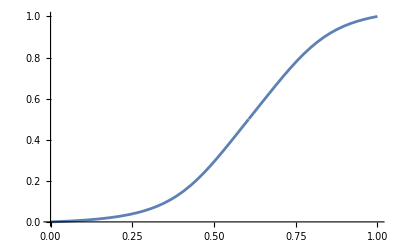

1/2+(2 (-20/33+x))/((1+(35937 (33/13)^(1/4) (-1+(140608 (13/33)^(1/4) √2)/35937) (-20/33+x)^(13/4))/2197)^(4/13))

1/2+(2 (-20/33+x))/((1-(476063 (-20/33+x)^3)/8000)^(1/3))

0.5+(2. (-0.606061+x))/((1.+69.8628 (-0.606061+x)^(13/4))^(4/13))

0.5+(2. (-0.606061+x))/((1.-59.5079 (-0.606061+x)^3)^(1/3))

-12.4739

4.02607

(0.842401 | 0.0424011 | 0.0424011
0.0784365 | 0.878437 | 0.0784365
0.0791624 | 0.0791624 | 0.879162)

(1.197 | -0.0530013 | -0.0530013
-0.0980456 | 1.15195 | -0.0980456
-0.098953 | -0.098953 | 1.15105)

```mathematica
(*Agx Config*)
kCompression=Rationalize[0.20];
kAgXMinEV=Rationalize[-10.0];
kAgXMaxEV=Rationalize[+6.5];
kAgXXPivot=Abs[kAgXMinEV/(kAgXMaxEV-kAgXMinEV)];
kAgXYPivot=Rationalize[0.50];
kLimitsContrast1=Rationalize[3.0];
kLimitsContrast2=Rationalize[3.25];
kGeneralContrast=Rationalize[2.0];

(*Constant*)
(*BT.709 truncates the CIE 1931 coordinates, It could also be {0.3127,0.3290} ?*)
kBT709D65xy=Rationalize[{0.31271,0.32902}];
kBT709Rxy=Rationalize[{0.64,0.33}];
kBT709Gxy=Rationalize[{0.3,0.6}];
kBT709Bxy=Rationalize[{0.15,0.06}];
colorspaceSRGB={xytoXYZ[kBT709Rxy],xytoXYZ[kBT709Gxy],xytoXYZ[kBT709Bxy]};
SSRGB=xytoXYZ[kBT709D65xy].Inverse[colorspaceSRGB];
SRGBtoXYZ={SSRGB[[1]]*colorspaceSRGB[[1]],SSRGB[[2]]*colorspaceSRGB[[2]],SSRGB[[3]]*colorspaceSRGB[[3]]};


(*AgX*)
equationScale[xPivot_,yPivot_,slopePivot_,power_]:=(
((slopePivot*xPivot)^(-power)) *
((slopePivot *xPivot/yPivot)^(power)-1)
)^(-1/power);

equationHyperbolic[x_,power_]:=
x/((1 + x^power)^(1/power));

equationTerm[x_,xPivot_,slopePivot_,scale_]:=
(slopePivot*(x-xPivot))/scale;

equationCurve[x_,xPivot_,yPivot_, slopePivot_,scale_]:=
If[scale<0,
scale*equationHyperbolic[
equationTerm[x,xPivot,slopePivot,scale],
kLimitsContrast1
]+yPivot,
scale*equationHyperbolic[
equationTerm[x,xPivot,slopePivot,scale],
kLimitsContrast2
]+yPivot
];

equationFullCurve[x_,xPivot_,yPivot_, slopePivot_]:=Module[
{scaleXPivot,scaleYPivot,toeScale,shoulderScale,scale},
scaleXPivot=If[x>=xPivot,1-xPivot,xPivot];
scaleYPivot=If[x>=xPivot,1-yPivot,yPivot];
toeScale=equationScale[scaleXPivot,scaleYPivot,slopePivot,kLimitsContrast1];
shoulderScale=equationScale[scaleXPivot,scaleYPivot,slopePivot,kLimitsContrast2];
scale=If[x>=xPivot,shoulderScale,-toeScale];
equationCurve[x,xPivot,yPivot,slopePivot,scale]
];

(*Calculate OpenColorIO allocation for log2 from open domain tristimulus value*)
calculateOCIOLog2[inEV_,odMiddleGrey_]:=
Log2[2^inEV*odMiddleGrey];

(*Colorspaces*)
(*http://www.brucelindbloom.com/index.html?Eqn_RGB_XYZ_Matrix.html*)
xytoXYZ[v_]:={v[[1]]/v[[2]],1,(1-v[[1]]-v[[2]])/v[[2]]};

AgXCompressedMatrix[compression_]:=Module[
{scaleFactor,AgXRxy,AgXGxy,AgXBxy,colorspaceAgXRGB,SAgXRGB,AgXRGBtoXYZ},
scaleFactor=1/(1-compression);
AgXRxy=(kBT709Rxy-kBT709D65xy)*scaleFactor+kBT709D65xy;
AgXGxy=(kBT709Gxy-kBT709D65xy)*scaleFactor+kBT709D65xy;
AgXBxy=(kBT709Bxy-kBT709D65xy)*scaleFactor+kBT709D65xy;

colorspaceAgXRGB={xytoXYZ[AgXRxy],xytoXYZ[AgXGxy],xytoXYZ[AgXBxy]};
SAgXRGB=xytoXYZ[kBT709D65xy].Inverse[colorspaceAgXRGB];
AgXRGBtoXYZ={SAgXRGB[[1]]*colorspaceAgXRGB[[1]],SAgXRGB[[2]]*colorspaceAgXRGB[[2]],SAgXRGB[[3]]*colorspaceAgXRGB[[3]]};
SRGBtoXYZ.Inverse[AgXRGBtoXYZ]
];

(*Debug*)
Plot[equationFullCurve[x,kAgXXPivot,kAgXYPivot, kGeneralContrast],{x,0,1}]
Assuming[x>=20/33,Simplify[equationFullCurve[x,kAgXXPivot,kAgXYPivot, kGeneralContrast]]]
Assuming[x<20/33,Simplify[equationFullCurve[x,kAgXXPivot,kAgXYPivot, kGeneralContrast]]]
Assuming[x>=20/33,N[Simplify[equationFullCurve[x,kAgXXPivot,kAgXYPivot, kGeneralContrast]],MachinePrecision]]
Assuming[x<20/33,N[Simplify[equationFullCurve[x,kAgXXPivot,kAgXYPivot, kGeneralContrast]],MachinePrecision]]
N[calculateOCIOLog2[kAgXMinEV,Rationalize[0.18]],MachinePrecision]
N[calculateOCIOLog2[kAgXMaxEV,Rationalize[0.18]],MachinePrecision]
kAgXCompressedMatrix=AgXCompressedMatrix[kCompression];
N[kAgXCompressedMatrix,MachinePrecision]//MatrixForm
N[Inverse[kAgXCompressedMatrix],MachinePrecision]//MatrixForm
```